# AdaptiveCellularAutomaton

One-line description explaining the function’s basic purpose

## Definition

```mathematica
ClearAll[TestCALifetime]
```

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
TestCALifetime[ca_List]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]
```

```mathematica
colorrules = {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]};
```

```mathematica
toassoc[mufuncspec_]:= If[!MatchQ[mufuncspec, _Rule] && !MatchQ[mufuncspec, List[_Rule..]]&&!AssociationQ[mufuncspec],
 <|"MutatedRule"-> getmutationfunction[mufuncspec, "Rule"]|>,
Association[KeyValueMap[StringJoin["Mutated", #1]-> getmutationfunction[#2, #1]&,Association[mufuncspec]]]]
```

```mathematica
tofunction[mufuncassoc_]:=
Association[ 
KeyValueMap[
Function[{key, val},key->val[#]], mufuncassoc]]&
```

```mathematica
getmutationfunction[args_,"Rule"]:= 
Which[IntegerQ[args], RandomRuleMutation[#Rule, args]&,
ListQ[args], RandomRuleMutation[#Rule, First[args], Sequence@@Rest[args]]&,
True, args]
```

```mathematica
getmutationfunction[args_, "InitialCondition"]:= 
Which[IntegerQ[args], InitialConditionMutation[#InitialCondition, args]&,
ListQ[args], InitialConditionMutation[#InitialCondition, First[args], Sequence@@Rest[args]]&,
True, args]
```

```mathematica
ClearAll[getcafunc];
getcafunc[evospec_,  stepspec_:Automatic]:= CellularAutomaton[If[KeyExistsQ[evospec["MutationFunction"],"MutatedRule"],#MutatedRule,evospec["StartingRule"]], If[KeyExistsQ[evospec["MutationFunction"],"MutatedInitialCondition"],#MutatedInitialCondition,evospec["StartingInitialCondition"]], If[stepspec === Automatic, evospec["Cut"], If[IntegerQ[stepspec] ||ListQ[stepspec], stepspec, stepspec[#]]]]&
```

```mathematica
ClearAll[getcafunc];
getcafunc[evospec_,  stepspec_:Automatic]:= CellularAutomaton[If[KeyExistsQ[evospec["MutationFunction"],"MutatedRule"],#MutatedRule,evospec["StartingRule"]], If[KeyExistsQ[evospec["MutationFunction"],"MutatedInitialCondition"],#MutatedInitialCondition,evospec["StartingInitialCondition"]], If[stepspec === Automatic, evospec["Cut"], If[IntegerQ[stepspec] ||ListQ[stepspec], stepspec, stepspec[#]]]]&
```

```mathematica
ClearAll@getfitnessfunction
getfitnessfunction[cafunc_, evospec_]:=Module[{}, 
If[evospec["FitnessFunction"] === "Lifetime", TestCALifetime[cafunc[#]]&,
evospec["FitnessFunction"][getcafunc[evospec][#]]&]]
```

```mathematica
getsequence[evos_, seqspec_]:= 
If[seqspec=== "Breakthroughs",GatherBy[evos, #Fitness&][[All, 1]], evos]
```

```mathematica
ClearAll[getpropertyfunction]
getpropertyfunction[evospec_, prop_]:= Replace[prop,
{"Plot"->(ArrayPlot[getcafunc[evospec][#]]&),
Rule["Plot", stepspec_]:> 
(ArrayPlot[getcafunc[evospec, stepspec][#]]&),
s_String:> (#[[s]]&),
l_List:> (#[[l]]&),
All:> (#[[All]]&),
o_:> o}
]
```

```mathematica
default = <|"StartingRule"->{0, 3, 1} , "StartingInitialCondition"->{{1}, 0},"Cut"->100,"Depth"->100,
"MutationFunction"->(<|"Rule"->(RandomRuleMutation[#Rule]&)|>), "FitnessFunction"->"Lifetime", "SelectionFunction"->(#MutatedFitness>=#Fitness&)|>;
```

```mathematica
ClearAll[AdaptiveCellularAutomaton]
AdaptiveCellularAutomaton[evospec_Association:default, sequencespec_String:"All", propertyspec_:{"Rule", "Fitness"}]:=Module[{},
merged = Join[default, evospec];
merged["MutationFunction"] = toassoc[merged["MutationFunction"]];
initialstate = 
<|"Rule"-> merged["StartingRule"],"InitialCondition"->merged["StartingInitialCondition"],"MutatedRule"->merged["StartingRule"], 
"MutatedInitialCondition"->None, "MutatedFitness"->None|>;
cafunc = getcafunc[evospec];
fitnessfunction = getfitnessfunction[cafunc, merged];
merged["MutationFunction"] = tofunction[merged["MutationFunction"]];
initialstate["Fitness"] = fitnessfunction[initialstate];
evos = 
If[sequencespec === "Final", Nest, NestList][
Block[{newstate = Join[#,merged["MutationFunction"][#]] },
newstate["MutatedFitness"] = fitnessfunction[newstate];
{newstate["Rule"], newstate["MutatedFitness"]};
If[merged["SelectionFunction"][newstate],newstate["Rule"] = newstate["MutatedRule"]; newstate["Fitness"] = newstate["MutatedFitness"]; newstate,
newstate]]&, initialstate, merged["Depth"]];
propertyfunction  = getpropertyfunction[merged,propertyspec];
If[sequencespec === "Final", propertyfunction@evos,propertyfunction/@ getsequence[evos, sequencespec]]]
```

## Documentation

### Usage

MyFunction[arg]

explanation of what use of the argument arg does.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Text about the example:

```mathematica
fitnessfunction
```

```mathematica
TestCALifetime[getcafunc[<|"StartingRule"->{0,4,1},"StartingInitialCondition"->{{1},0},"Cut"->100,"Depth"->2000,"MutationFunction"-><|"MutatedRule"->(RandomRuleMutation[#Rule]&)|>,"FitnessFunction"->"Lifetime","SelectionFunction"->(#MutatedFitness≥#Fitness&)|>][#1]]&
```

```mathematica
merged["MutationFunction"]
```

Association[KeyValueMap[Function[{key,val},key→val[#1]],<|MutatedRule→(RandomRuleMutation[#Rule]&)|>]]&

```mathematica
evos
```

{<|Rule→{0,3,1},InitialCondition→{{1},0},MutatedRule→None,MutatedInitialCondition→None,MutatedFitness→None,Fitness→1|>,<|Rule→{31381059609,3,1},InitialCondition→{{1},0},MutatedRule→{31381059609,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{313810596090,3,1},InitialCondition→{{1},0},MutatedRule→{313810596090,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{5397542252748,3,1},InitialCondition→{{1},0},MutatedRule→{5397542252748,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{5397542292114,3,1},InitialCondition→{{1},0},MutatedRule→{5397542292114,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{5397547075083,3,1},InitialCondition→{{1},0},MutatedRule→{5397547075083,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{5397561423990,3,1},InitialCondition→{{1},0},MutatedRule→{5397561423990,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{5397561424152,3,1},InitialCondition→{{1},0},MutatedRule→{5397561424152,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{5397556641183,3,1},InitialCondition→{{1},0},MutatedRule→{5397556641183,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{5397944061672,3,1},InitialCondition→{{1},0},MutatedRule→{5397944061672,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{5397944179770,3,1},InitialCondition→{{1},0},MutatedRule→{5397944179770,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>}

```mathematica
propertyfunction
```

All

```mathematica
fitnessfunction
```

TestCALifetime[getcafunc[<|StartingRule→{0,3,1},StartingInitialCondition→{{1},0},Cut→10,Depth→10,MutationFunction→<|MutatedRule→(RandomRuleMutation[#Rule]&)|>,FitnessFunction→Lifetime,SelectionFunction→(#MutatedFitness≥#Fitness&)|>][#1]]&

```mathematica
fitnessfunction[evos[[9]]]
```

1

```mathematica
evos
```

{<|Rule→{0,3,1},InitialCondition→{{1},0},MutatedRule→None,MutatedInitialCondition→None,MutatedFitness→None,Fitness→1|>,<|Rule→{1062882,3,1},InitialCondition→{{1},0},MutatedRule→{1062882,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>,<|Rule→{10461416085,3,1},InitialCondition→{{1},0},MutatedRule→{10461416085,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>}

```mathematica
Table[SeedRandom[2422 + i];AdaptiveCellularAutomaton[<|"StartingRule"->{0, 4, 1}, "Depth"->10, "Cut"->100|>,"All", "MutatedFitness"] , {i, 10}]
```

{{None,1,1,1,1,1,1,2,2,2,2},{None,1,1,1,1,1,1,1,1,1,1},{None,1,1,1,1,1,1,1,1,-∞,-∞},{None,1,1,1,1,1,1,1,1,1,1},{None,1,1,1,1,1,1,1,1,1,1},{None,1,1,1,2,2,2,2,2,2,2},{None,1,1,1,1,1,1,1,1,1,1},{None,1,1,1,1,1,1,1,1,1,1},{None,1,1,1,1,1,1,1,2,2,2},{None,1,1,1,1,1,1,1,1,1,1}}

KeyExistsQ::invrl: The argument Association[KeyValueMap[Function[{key,val},key→val[#1]],<|MutatedRule→(RandomRuleMutation[#Rule]&)|>]]& is not a valid Association or a list of rules.

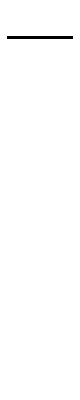

```mathematica
SeedRandom[222332];AdaptiveCellularAutomaton[<|"StartingRule"->{0, 4, 1}, "Depth"->1000, "Cut"->100|>, "Final", "Plot"]
```

```mathematica
SeedRandom[2422 + 1];AdaptiveCellularAutomaton[<|"StartingRule"->{0, 4, 1}, "Depth"->100, "Cut"->100|>]
```

{<|Rule→{0,4,1},Fitness→1|>,<|Rule→{1329227995784915872903807060280344576,4,1},Fitness→1|>,<|Rule→{1329227995804258686017641127075643392,4,1},Fitness→1|>,<|Rule→{1329228055225380571715894322233606144,4,1},Fitness→1|>,<|Rule→{1329228055225380571733908720743088128,4,1},Fitness→1|>,<|Rule→{1329228055225380574039751729956782080,4,1},Fitness→1|>,<|Rule→{1329228055225380574039751729956782092,4,1},Fitness→1|>,<|Rule→{1329228689050680688154452478308384780,4,1},Fitness→2|>,<|Rule→{1329228689050680688154452478308450316,4,1},Fitness→2|>,<|Rule→{1329228689050680688730913230611873804,4,1},Fitness→2|>,<|Rule→{1329228689050680688730930822797918220,4,1},Fitness→2|>,<|Rule→{1329228689050680688730930822797950988,4,1},Fitness→2|>,<|Rule→{1329228689050680688730930960236904460,4,1},Fitness→2|>,<|Rule→{1329228689050680688730930891517427724,4,1},Fitness→2|>,<|Rule→{1329228689050680688730930892322734092,4,1},Fitness→2|>,<|Rule→{1329228669243640060164846493936746508,4,1},Fitness→2|>,<|Rule→{22596876601802294026625759458422259724,4,1},Fitness→2|>,<|Rule→{22596957731440708633307455247427403788,4,1},Fitness→2|>,<|Rule→{22596957731440708633307455247494512652,4,1},Fitness→2|>,<|Rule→{22596957731440708633307455247495036940,4,1},Fitness→2|>,<|Rule→{22596957731421365820193621180699738124,4,1},Fitness→2|>,<|Rule→{22596957731421365820481851556851449868,4,1},Fitness→2|>,<|Rule→{22596957731421365820481851591211188236,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807628,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>,<|Rule→{22596957731421366041842780475725807620,4,1},Fitness→2|>}

```mathematica
Dataset[evos]
```

```mathematica
cafunc
```

CellularAutomaton[If[KeyExistsQ[<|StartingRule→{0,4,1},StartingInitialCondition→{{1},0},Cut→100,Depth→1,MutationFunction→<|MutatedRule→(RandomRuleMutation[#Rule]&)|>,FitnessFunction→Lifetime,SelectionFunction→(#MutatedFitness≥#Fitness&)|>[MutationFunction],MutatedRule],#Rule,<|StartingRule→{0,4,1},StartingInitialCondition→{{1},0},Cut→100,Depth→1,MutationFunction→<|MutatedRule→(RandomRuleMutation[#Rule]&)|>,FitnessFunction→Lifetime,SelectionFunction→(#MutatedFitness≥#Fitness&)|>[StartingRule]],If[KeyExistsQ[<|StartingRule→{0,4,1},StartingInitialCondition→{{1},0},Cut→100,Depth→1,MutationFunction→<|MutatedRule→(RandomRuleMutation[#Rule]&)|>,FitnessFunction→Lifetime,SelectionFunction→(#MutatedFitness≥#Fitness&)|>[MutationFunction],MutatedInitialCondition],#InitialCondition,<|StartingRule→{0,4,1},StartingInitialCondition→{{1},0},Cut→100,Depth→1,MutationFunction→<|MutatedRule→(RandomRuleMutation[#Rule]&)|>,FitnessFunction→Lifetime,SelectionFunction→(#MutatedFitness≥#Fitness&)|>[StartingInitialCondition]],If[Automatic===Automatic,<|StartingRule→{0,4,1},StartingInitialCondition→{{1},0},Cut→100,Depth→1,MutationFunction→<|MutatedRule→(RandomRuleMutation[#Rule]&)|>,FitnessFunction→Lifetime,SelectionFunction→(#MutatedFitness≥#Fitness&)|>[Cut],If[IntegerQ[Automatic]||ListQ[Automatic],Automatic,Automatic[#1]]]]&

```mathematica
Dataset[evos[[20;;30]]]
```

```mathematica
fitnessfunction/@ evos
```

{1,1,1,1,2,2,2,2,2,2,2}

```mathematica
evos[[{5}]]
```

{<|Rule→{54043195545256704,4,1},InitialCondition→{{1},0},MutatedRule→{54043195545256704,4,1},MutatedInitialCondition→None,MutatedFitness→2,Fitness→2|>}

```mathematica
evos[[{6}]]
```

{<|Rule→{54043195545256704,4,1},InitialCondition→{{1},0},MutatedRule→{83076749736557242110531136812778240,4,1},MutatedInitialCondition→None,MutatedFitness→-∞,Fitness→2|>}

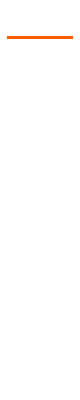
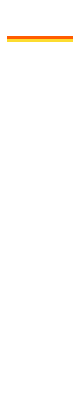
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[#Rule, {{1},0}, 100], ColorRules-> colorrules]&/@ evos
```

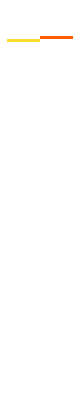
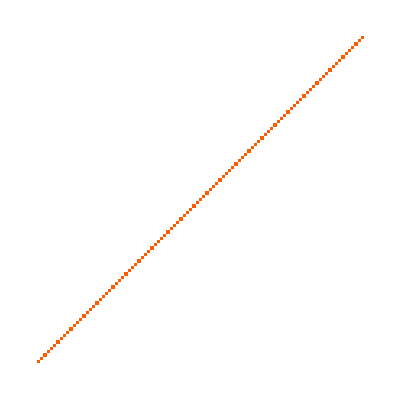
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[#Rule, {{1},0}, 100], ColorRules-> colorrules]&/@ evos[[20;;30]]
```

```mathematica
fitnessfunction[initialstate]
```

Function::slota: Named Slot InitialCondition in CellularAutomaton[«1»,«1»,If[Automatic===Automatic,<|StartingRule→{0,3},«5»,SelectionFunction→(#MutatedFitness≥#Fitness&)|>[S…c],If[IntegerQ[Automatic]||ListQ[Automatic],Automatic,Automatic[#1]]]]& cannot be filled from <|Rule→{0,3},IniitalCondition→{{1},0},MutatedRule→None,MutatedInitialCondition→None,MutatedFitness→None,Fitness→[◼] | TestCALifeTime [Missing[KeyAbsent,StartingInitialConditions],#2]|>.

1

```mathematica
MyFunction[x,y]
```

x y

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.